# Functions

Import a lattice

```mathematica
importLatt[file_,species_]:=Module[
{latt,latt2}
,
SetDirectory[NotebookDirectory[]];

latt=Map[ToExpression@StringSplit[#][[;;3]]&,Select[ReadList[file,String],StringTake[#,-1]==species&]];
latt2=SparseArray[Map[#->1&,latt],{10,10,10},0];

Return[latt2];
];
```

```mathematica
importLattAll[file_]:=Module[
{ass}
,
ass=Association[];
ass["A"]=importLatt[file,"A"];
ass["B"]=importLatt[file,"B"];
ass["C"]=importLatt[file,"C"];
Return[ass];
];
```

Get count, NNs of lattice

```mathematica
getNNsAtTime[fnames_,species1_,species2_]:=Module[
{ave,std,latt1,latt2},
ave=0.0;
Do[
latt1=importLatt[fname,species1];
latt2=importLatt[fname,species2];
Do[
If[i+1≤10,
If[(latt1[[i,j,k]]==1&&latt2[[i+1,j,k]]==1)||(latt2[[i,j,k]]==1&&latt1[[i+1,j,k]]==1),ave+=1];
];
If[j+1≤10,
If[(latt1[[i,j,k]]==1&&latt2[[i,j+1,k]])||(latt2[[i,j,k]]==1&&latt1[[i,j+1,k]])==1,ave+=1];
];
If[k+1≤10,
If[(latt1[[i,j,k]]==1&&latt2[[i,j,k+1]]==1)||(latt2[[i,j,k]]==1&&latt1[[i,j,k+1]]==1),ave+=1];
];
,{i,1,10},{j,1,10},{k,1,10}]

,{fname,fnames}];
ave/=Length[fnames];

Return[ave]
];
```

```mathematica
getCountAtTime[fnames_,species_]:=Module[
{ave},
ave=0.0;
Do[
ave+=Total[Total[Total[importLatt[fname,species]]]];

,{fname,fnames}];
ave/=Length[fnames];

Return[ave]
];
```

Get filenames

```mathematica
getFnamesAtTime[t_,noVersions_]:=Table["../data/sample/"<>IntegerString[t,10,4]<>"/layer_0_"<>IntegerString[v,10,4]<>".txt",{v,0,noVersions-1}];
```

```mathematica
getFnamesAtTimeSS[t_,noVersions_]:=Table["../../rossler_stoch_sims/data/lattice_v"<>IntegerString[v,10,3]<>"/lattice/"<>IntegerString[t,10,4]<>".txt",{v,1,noVersions}];
```

# Moments

Parameters

```mathematica
tmin=0;
tmax=100;
noVersions=100;
```

Counts

### A

```mathematica
countsA=Association[];
```

```mathematica
Monitor[
Do[
countsA[t]=getCountAtTime[getFnamesAtTime[t,noVersions],"A"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

```mathematica
countsAss=Association[];
```

```mathematica
Monitor[
Do[
countsAss[t]=getCountAtTime[getFnamesAtTimeSS[t,noVersions],"A"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

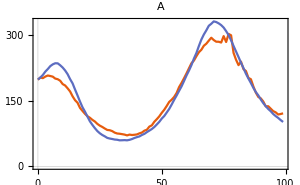

```mathematica
pltA=ListLinePlot[{countsA[[;;-2]],countsAss[[;;-2]]},PlotLabel->"A",ImageSize->300,FrameTicks->{{{0,150,300},{}},{{0,50,100},{}}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/mom_a.pdf",pltA]
```

../figures/mom_a.pdf

### B

```mathematica
countsB=Association[];
```

```mathematica
Monitor[
Do[
countsB[t]=getCountAtTime[getFnamesAtTime[t,noVersions],"B"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

```mathematica
countsBss=Association[];
```

```mathematica
Monitor[
Do[
countsBss[t]=getCountAtTime[getFnamesAtTimeSS[t,noVersions],"B"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

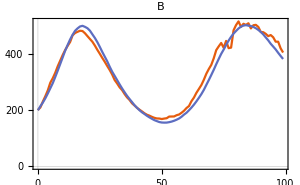

```mathematica
pltB=ListLinePlot[{countsB[[;;-2]],countsBss[[;;-2]]},PlotLabel->"B",ImageSize->300,FrameTicks->{{{0,200,400},{}},{{0,50,100},{}}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/mom_b.pdf",pltB]
```

../figures/mom_b.pdf

### C

```mathematica
countsC=Association[];
```

```mathematica
Monitor[
Do[
countsC[t]=getCountAtTime[getFnamesAtTime[t,noVersions],"C"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

```mathematica
countsCss=Association[];
```

```mathematica
Monitor[
Do[
countsCss[t]=getCountAtTime[getFnamesAtTimeSS[t,noVersions],"C"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

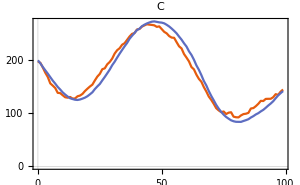

```mathematica
pltC=ListLinePlot[{countsC[[;;-2]],countsCss[[;;-2]]},PlotLabel->"C",ImageSize->300,FrameTicks->{{{0,100,200},{}},{{0,50,100},{}}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/mom_c.pdf",pltC]
```

../figures/mom_c.pdf

NNs

### AA

```mathematica
nnsAA=Association[];
```

```mathematica
Monitor[
Do[
nnsAA[t]=getNNsAtTime[getFnamesAtTime[t,noVersions],"A","A"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

```mathematica
nnsAAss=Association[];
```

```mathematica
Monitor[
Do[
nnsAAss[t]=getNNsAtTime[getFnamesAtTimeSS[t,noVersions],"A","A"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

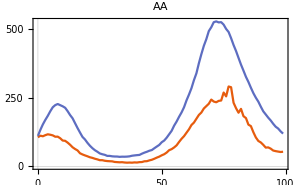

```mathematica
pltAA=ListLinePlot[{nnsAA[[;;-2]],nnsAAss[[;;-2]]},PlotLabel->"AA",ImageSize->300,FrameTicks->{{{0,250,500,1000},{}},{{0,50,100},{}}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/mom_aa.pdf",pltAA]
```

../figures/mom_aa.pdf

### BB

```mathematica
nnsBB=Association[];
```

```mathematica
Monitor[
Do[
nnsBB[t]=getNNsAtTime[getFnamesAtTime[t,noVersions],"B","B"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

```mathematica
nnsBBss=Association[];
```

```mathematica
Monitor[
Do[
nnsBBss[t]=getNNsAtTime[getFnamesAtTimeSS[t,noVersions],"B","B"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

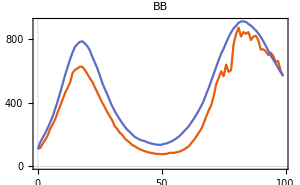

```mathematica
pltBB=ListLinePlot[{nnsBB[[;;-2]],nnsBBss[[;;-2]]},PlotLabel->"BB",ImageSize->300,FrameTicks->{{{0,400,800,1000},{}},{{0,50,100},{}}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/mom_bb.pdf",pltBB]
```

../figures/mom_bb.pdf

### BB

```mathematica
nnsCC=Association[];
```

```mathematica
Monitor[
Do[
nnsCC[t]=getNNsAtTime[getFnamesAtTime[t,noVersions],"C","C"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

```mathematica
nnsCCss=Association[];
```

```mathematica
Monitor[
Do[
nnsCCss[t]=getNNsAtTime[getFnamesAtTimeSS[t,noVersions],"C","C"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

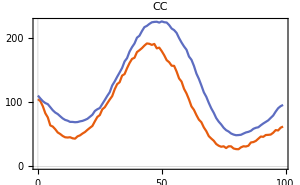

```mathematica
pltCC=ListLinePlot[{nnsCC[[;;-2]],nnsCCss[[;;-2]]},PlotLabel->"CC",ImageSize->300,FrameTicks->{{{0,100,200},{}},{{0,50,100},{}}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/mom_cc.pdf",pltCC]
```

../figures/mom_cc.pdf

### AB

```mathematica
nnsAB=Association[];
```

```mathematica
Monitor[
Do[
nnsAB[t]=getNNsAtTime[getFnamesAtTime[t,noVersions],"A","B"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

```mathematica
nnsABss=Association[];
```

```mathematica
Monitor[
Do[
nnsABss[t]=getNNsAtTime[getFnamesAtTimeSS[t,noVersions],"A","B"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

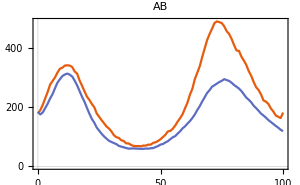

```mathematica
pltAB=ListLinePlot[{nnsAB,nnsABss},PlotLabel->"AB",ImageSize->300,FrameTicks->{{{0,200,400},{}},{{0,50,100},{}}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/mom_ab.pdf",pltAB]
```

../figures/mom_ab.pdf

### AC

```mathematica
nnsAC=Association[];
```

```mathematica
Monitor[
Do[
nnsAC[t]=getNNsAtTime[getFnamesAtTime[t,noVersions],"A","C"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

```mathematica
nnsACss=Association[];
```

```mathematica
Monitor[
Do[
nnsACss[t]=getNNsAtTime[getFnamesAtTimeSS[t,noVersions],"A","C"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

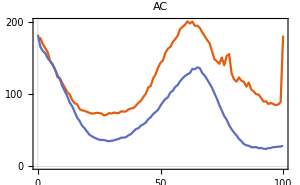

```mathematica
pltAC=ListLinePlot[{nnsAC,nnsACss},PlotLabel->"AC",ImageSize->300,FrameTicks->{{{0,100,200},{}},{{0,50,100},{}}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/mom_ac.pdf",pltAC]
```

../figures/mom_ac.pdf

### BC

```mathematica
nnsBC=Association[];
```

```mathematica
Monitor[
Do[
nnsBC[t]=getNNsAtTime[getFnamesAtTime[t,noVersions],"B","C"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

```mathematica
nnsBCss=Association[];
```

```mathematica
Monitor[
Do[
nnsBCss[t]=getNNsAtTime[getFnamesAtTimeSS[t,noVersions],"B","C"];
,{t,tmin,tmax}];
,ProgressIndicator[t,{tmin,tmax}]];
```

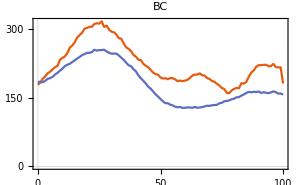

```mathematica
pltBC=ListLinePlot[{nnsBC,nnsBCss},PlotLabel->"BC",ImageSize->300,FrameTicks->{{{0,150,300},{}},{{0,50,100},{}}}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/mom_bc.pdf",pltBC]
```

../figures/mom_bc.pdf

# Legend

```mathematica
leg=LineLegend[{ColorData[97,2],ColorData[97,1]},{"Reduced Model","Stoch. Sim."},LabelStyle->{FontSize->28}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
If[!DirectoryQ["../figures"],CreateDirectory["../figures"]];
Export["../figures/leg.pdf",leg]
```

../figures/leg.pdf